## Constants, Units and Parameters

```mathematica
Needs["NumericalCalculus`"]
Needs["ErrorBarPlots`"];
Hz=1;kHz=10^3;MHz=10^6;GHz=10^9;THz=10^12;
m=1;cm=10^-2;mm=10^-3;μm=10^-6;nm=10^-9;pm=10^-12;
s=1;ms=10^-3;μs=10^-6;ns=10^-9;ps=10^-12;
Gauss=10^-4;mG=10^-3 Gauss;μG=10^-6 Gauss;T=1;
mW=10^-3;μW=10^-6;
c=2.99792458 10^8 m/s;
μ0=4π 10^-7;
ϵ0=1/(μ0 c^2);
h=6.62606896 10^-34;
ℏ=h/(2π);
e=1.602176487 10^-19;
μB=9.27400915 10^-24;
AMU=1.660538782 10^-27;
AME=9.10938215 10^-31;
a0=0.52917720859 10^-10 m;
kB=1.3806504 10^-23;
Kelvin=1;μK=10^-6 Kelvin;nK=10^-9 Kelvin;

AbundanceK39=93.2581 0.01;
AbundanceK40=0.0117 0.01;
AbundanceK41=6.7302 0.01;
massK39=38.96370668AMU;
massK40=39.96399848AMU;
massK41=40.96182576 AMU;
Meltingpoint=336.8K;
Boilingpoint=1047.15K;

λD1K40=770.108136507nm;
ΓD1K40=2π 5.956MHz;
ωD1K40=c/λD1K40 2π;
λD2K40=766.700674872nm;
ΓD2K40=2π 6.035MHz;
ωD2K40=c/λD2K40 2π;

AhfGroundK40=-285.7308MHz;
AhfD1K40=-34.523MHz;
AhfD2K40=-7.585MHz;
BhfD2K40=-3.445MHz;
gs=2.0023193043622;
gIK40=0.000176490;
gJGround=2.00229421;
gJD1=2./3;
gJD2=4./3;

λtrap=1053.57nm;
ωtrap=c/λtrap 2π;
λlat=λtrap;
ωlat=ωtrap;
klat=(2π)/λlat;
Erecoil=(ℏ^2 klat^2)/(2 massK40);
```

## lattice parameters

```mathematica
(*Lattice parameters*)
```

```mathematica
Vlatx=2.5;(*unit: Er*)
Vlaty=Vlatx;
Vlatz=Vlatx;
bandnumber=6;

(*angles*)
(*-Graphics-*)
θxdt1=57.15/180 π;θxdt2=29.24/180 π;θxlat=30.17/180 π;θylat=31.54/180 π;
vecxdt1=({{Cos[θxdt1]}, {-Sin[θxdt1]}});vecxlat=({{Sin[θxlat]}, {Cos[θxlat]}});vecylat=({{Cos[θylat]}, {-Sin[θylat]}});
Clear[hh,kk];
solangle=Solve[hh+kk*(Sin[θxlat]*Cos[θylat]-Cos[θxlat]*Sin[θylat])==Cos[θxdt1]*Sin[θxlat]-Sin[θxdt1]Cos[θxlat]&&
hh*(Sin[θxlat]*Cos[θylat]-Cos[θxlat]*Sin[θylat])+kk==Cos[θxdt1]*Cos[θylat]+Sin[θxdt1]Sin[θylat],{hh,kk}]
xdt1toxlat=solangle⟦1,1,2⟧
xdt1toylat=solangle⟦1,2,2⟧
```

{{hh→-0.432367,kk→0.89142}}

-0.432367

0.89142

### do not project along one lattice direction. Assumption : isotropic cubic lattice

```mathematica
xdt1toxlat=1;
xdt1toylat=0;
```

## overall trap frequency (including harmonic confinement of lattice beams)

```mathematica
λlat=1054nm;
klat=(2π)/λlat;
Er=(ℏ^2 klat^2)/(2 massK40);
w0x=60μm;
w0y=60μm;
w0z=85μm;

xdt1=0.5;
xdtfreq=√(xdt1*1000)*3.29116-15.03525
xdtfreq=32;


fx=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatz Er-√(Vlatz Er Er))/w0z^2))/(2π)
fy=√(2/massK40((2Vlatz Er-√(Vlatz Er Er))/w0z^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π)
fz=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π)
f0= √(1*xdtfreq^2+fx^2)
```

58.5573

56.8725

56.8725

65.7086

65.257

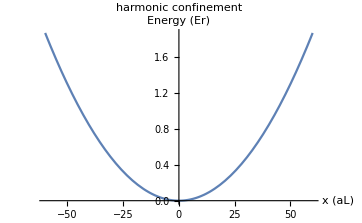

```mathematica
potential[x_,f0x_]:=1/2 massK40 (2π f0x)^2(x λlat/2)^2/Erecoil;
Plot[potential[x,f0],{x,-60,60},PlotLabel->"harmonic confinement",AxesLabel->{"x (aL)","Energy (Er)"}]
```

```mathematica
onsiteU=0.407634 h kHz/Erecoil (174(1-7.5/(206-202.1)))/174 
tunnelling= 0.12642;(*unit is Erecoil*)
tempβ=4;
(*1/(kB Temp) = 1/Er*)
```

-0.0836618

## density fitting

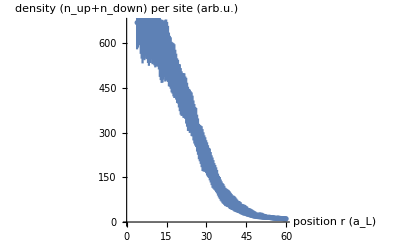

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

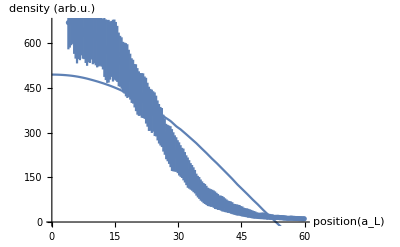

{{1.01833,-0.979078,1999.98,-286.809,2799.77,0.252392,176.048,49.4857}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.979078 | 0.252392 | -3.87919 | 0.000152128
ampx | 1999.98 | 176.048 | 11.3605 | 2.28024×10^-22
offsetx | -286.809 | 49.4857 | -5.79581 | 3.45546×10^-8

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

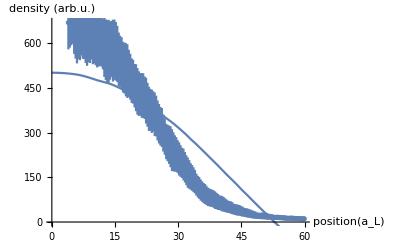

{{1.0627,-0.970244,1999.99,-268.041,2816.,0.173371,144.376,36.3586}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.970244 | 0.173371 | -5.59635 | 9.15034×10^-8
ampx | 1999.99 | 144.376 | 13.8527 | 2.74779×10^-29
offsetx | -268.041 | 36.3586 | -7.37215 | 8.16908×10^-12

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

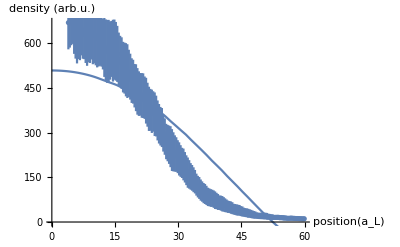

{{1.11111,-0.942779,1999.99,-254.509,2945.1,0.192398,163.469,37.5988}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.942779 | 0.192398 | -4.90016 | 2.30524×10^-6
ampx | 1999.99 | 163.469 | 12.2347 | 8.56026×10^-25
offsetx | -254.509 | 37.5988 | -6.76907 | 2.2589×10^-10

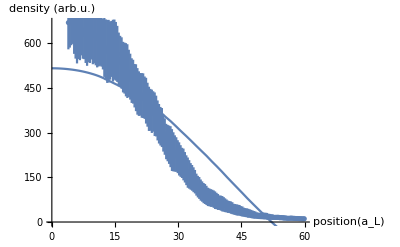

{{1.16414,-0.926537,2000.,-236.253,2930.41,0.175679,164.071,33.4846}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.926537 | 0.175679 | -5.27404 | 4.21821×10^-7
ampx | 2000. | 164.071 | 12.1898 | 1.14048×10^-24
offsetx | -236.253 | 33.4846 | -7.05557 | 4.74842×10^-11

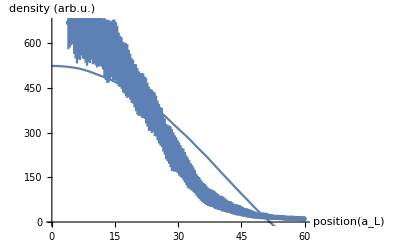

{{1.22249,-0.887539,1999.83,-225.019,3082.68,0.172947,173.506,31.781}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.887539 | 0.172947 | -5.13184 | 8.12553×10^-7
ampx | 1999.83 | 173.506 | 11.526 | 7.93735×10^-23
offsetx | -225.019 | 31.781 | -7.0803 | 4.1441×10^-11

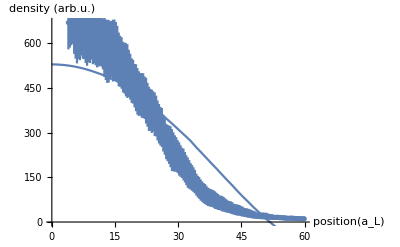

{{1.287,-0.888026,2000.,-198.712,2748.59,0.1692,185.478,29.3052}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.888026 | 0.1692 | -5.24838 | 4.75196×10^-7
ampx | 2000. | 185.478 | 10.7829 | 8.93758×10^-21
offsetx | -198.712 | 29.3052 | -6.78078 | 2.12087×10^-10

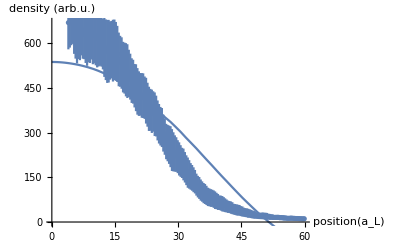

{{1.3587,-0.863453,2000.,-180.754,2646.77,0.149648,179.67,25.6514}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.863453 | 0.149648 | -5.7699 | 3.92596×10^-8
ampx | 2000. | 179.67 | 11.1315 | 9.78727×10^-22
offsetx | -180.754 | 25.6514 | -7.04655 | 4.98996×10^-11

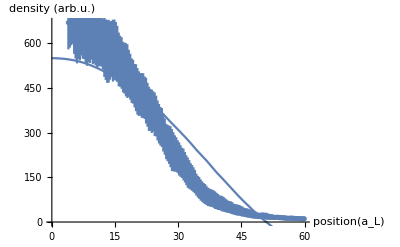

{{1.43885,-0.809444,1999.91,-173.161,2908.46,0.147806,197.294,23.684}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.809444 | 0.147806 | -5.47641 | 1.62675×10^-7
ampx | 1999.91 | 197.294 | 10.1367 | 5.23064×10^-19
offsetx | -173.161 | 23.684 | -7.31129 | 1.1491×10^-11

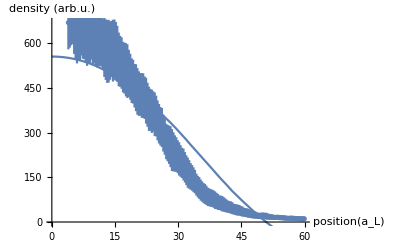

{{1.52905,-0.7955,2000.,-148.768,2502.53,0.127265,185.319,20.393}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.7955 | 0.127265 | -6.25074 | 3.47679×10^-9
ampx | 2000. | 185.319 | 10.7922 | 8.42774×10^-21
offsetx | -148.768 | 20.393 | -7.29507 | 1.25821×10^-11

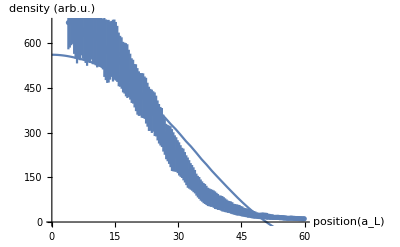

{{1.63132,-0.775158,2000.,-125.888,2083.43,0.0949642,151.957,16.2711}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.775158 | 0.0949642 | -8.16263 | 8.69302×10^-14
ampx | 2000. | 151.957 | 13.1616 | 2.26803×10^-27
offsetx | -125.888 | 16.2711 | -7.73692 | 1.02903×10^-12

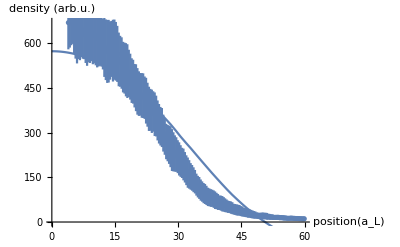

{{1.74825,-0.731201,2000.,-111.836,1962.43,0.0817817,146.002,13.8141}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.731201 | 0.0817817 | -8.9409 | 8.36028×10^-16
ampx | 2000. | 146.002 | 13.6984 | 7.3461×10^-29
offsetx | -111.836 | 13.8141 | -8.09581 | 1.28579×10^-13

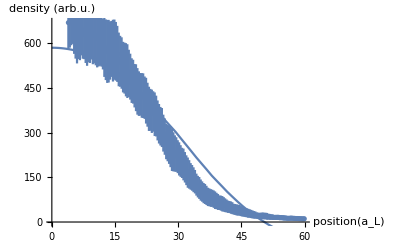

{{1.88324,-0.692433,2000.,-95.142,1685.9,0.0757252,148.479,12.0801}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.692433 | 0.0757252 | -9.14403 | 2.43131×10^-16
ampx | 2000. | 148.479 | 13.4699 | 3.15932×10^-28
offsetx | -95.142 | 12.0801 | -7.87593 | 4.6194×10^-13

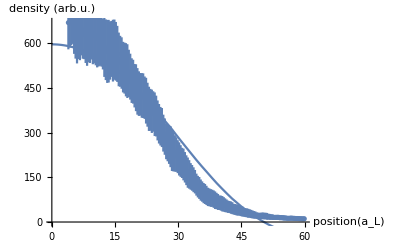

{{2.04082,-0.650604,2000.,-78.4421,1385.54,0.0606626,130.572,9.92056}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.650604 | 0.0606626 | -10.725 | 1.28956×10^-20
ampx | 2000. | 130.572 | 15.3172 | 2.57899×10^-33
offsetx | -78.4421 | 9.92056 | -7.90703 | 3.85827×10^-13

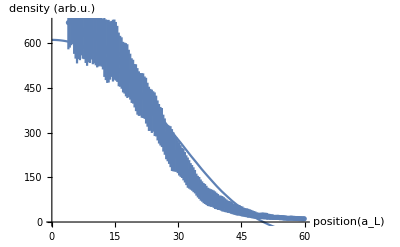

{{2.22717,-0.604125,2000.,-63.5257,1118.74,0.0440328,107.014,7.60242}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.604125 | 0.0440328 | -13.7199 | 6.40635×10^-29
ampx | 2000. | 107.014 | 18.6891 | 2.80065×10^-42
offsetx | -63.5257 | 7.60242 | -8.35599 | 2.78129×10^-14

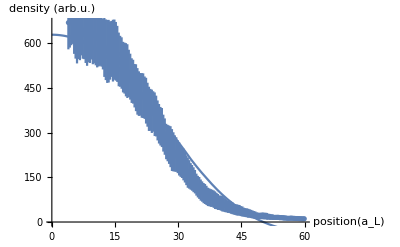

{{2.45098,-0.55577,2000.,-49.152,845.596,0.0398925,107.95,6.2169}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.55577 | 0.0398925 | -13.9317 | 1.66071×10^-29
ampx | 2000. | 107.95 | 18.5272 | 7.33641×10^-42
offsetx | -49.152 | 6.2169 | -7.90619 | 3.87719×10^-13

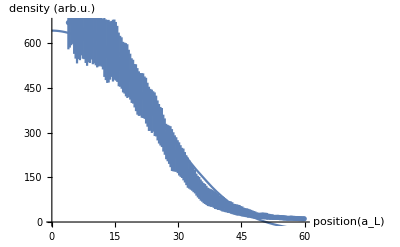

{{2.7248,-0.509237,2000.,-32.7988,515.156,0.0308334,92.5571,4.72606}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.509237 | 0.0308334 | -16.5158 | 1.47156×10^-36
ampx | 2000. | 92.5571 | 21.6083 | 1.39594×10^-49
offsetx | -32.7988 | 4.72606 | -6.93998 | 8.94424×10^-11

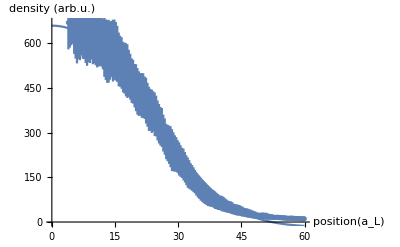

{{3.06748,-0.461218,2000.,-17.5878,252.568,0.0188037,62.8905,3.07086}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.461218 | 0.0188037 | -24.5281 | 2.01793×10^-56
ampx | 2000. | 62.8905 | 31.8013 | 1.50068×10^-71
offsetx | -17.5878 | 3.07086 | -5.72731 | 4.83922×10^-8

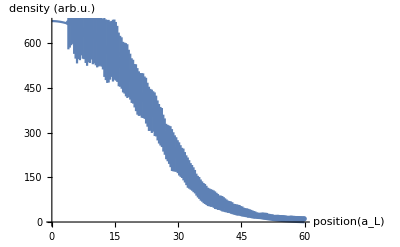

{{3.50877,-0.414005,2000.,-2.7542,68.0252,0.00786687,28.6019,1.68552}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.414005 | 0.00786687 | -52.6264 | 8.80479×10^-104
ampx | 2000. | 28.6019 | 69.9255 | 6.26161×10^-123
offsetx | -2.7542 | 1.68552 | -1.63404 | 0.104193

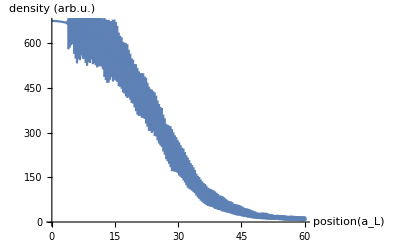

{{4.09836,-0.307741,1776.11,7.11083,11.3184,0.00522199,17.0781,1.24493}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.307741 | 0.00522199 | -58.9317 | 2.38044×10^-111
ampx | 1776.11 | 17.0781 | 103.999 | 3.07976×10^-150
offsetx | 7.11083 | 1.24493 | 5.71185 | 5.21954×10^-8

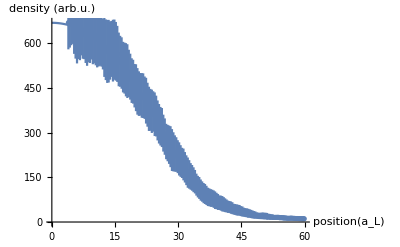

{{4.92611,-0.209882,1584.26,15.7529,9.35378,0.00296521,8.55584,0.874477}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.209882 | 0.00296521 | -70.7814 | 9.28157×10^-124
ampx | 1584.26 | 8.55584 | 185.167 | 1.8073×10^-190
offsetx | 15.7529 | 0.874477 | 18.0141 | 1.58327×10^-40

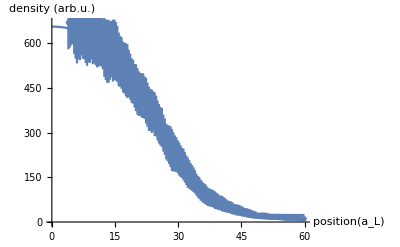

{{6.17284,-0.12665,1433.66,23.3583,59.0758,0.00308014,7.79109,1.16297}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.12665 | 0.00308014 | -41.1182 | 1.24309×10^-87
ampx | 1433.66 | 7.79109 | 184.012 | 4.95569×10^-190
offsetx | 23.3583 | 1.16297 | 20.085 | 7.90991×10^-46

InterpolatingFunction::dmval: Input value {7.94777} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7.94632} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

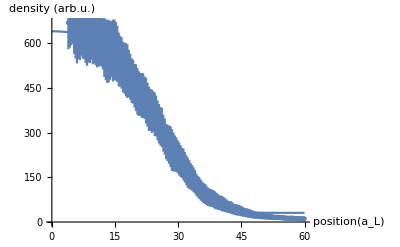

{{8.26446,-0.0631162,1331.75,30.739,165.963,0.00357944,8.56454,1.74316}}

| Estimate | Standard Error | t-Statistic | P-Value
μx | -0.0631162 | 0.00357944 | -17.633 | 1.58096×10^-39
ampx | 1331.75 | 8.56454 | 155.496 | 2.98738×10^-178
offsetx | 30.739 | 1.74316 | 17.6341 | 1.57038×10^-39

```mathematica
(*data input*)
startid=12;

rawdatatemp=ToExpression[Import["D:\\Documents\\MC fitting\\2.5Er 206G\\temp.txt","TSV"]];

datainput1=Table[{rawdatatemp⟦ii,1⟧(0.18μm)/(λlat/2),rawdatatemp⟦ii,2⟧,rawdatatemp⟦ii,3⟧},{ii,startid,Length[rawdatatemp]}];
datainput=Select[datainput1,#⟦1⟧≤ 60&];
ErrorListPlot[datainput,AxesLabel->{"position r (a_L)","density (n_up+n_down) per site (arb.u.)"}]
(*MC data input*)
path=NotebookDirectory[];
path=StringJoin[path,"\\results.txt"];
resulttemp=ToExpression[Import[path,"TSV"]];
result=resulttemp;
tempβlist=Union[result⟦All,1⟧];
tempβnum=Length[tempβlist];

(*fitting*)

fitls={{0}};

For[iitempβ=1,iitempβ≤tempβnum,iitempβ++,
{
tempβcheck=tempβlist⟦iitempβ⟧;
Tβlist= Select[result,#⟦1⟧==tempβcheck&]⟦All,1;;6⟧;

densitycheckfunc=Interpolation[Tβlist⟦All,{2,3}⟧];
densityerrcheckfunc=Interpolation[Tβlist⟦All,{2,4}⟧];
doubloncheckfunc=Interpolation[Tβlist⟦All,{2,5}⟧];
doublonerrcheckfunc=Interpolation[Tβlist⟦All,{2,6}⟧];

finalρfunc[positionxx_,μfitxx_,ampxx_,offsetxx_]:=ampxx*(densitycheckfunc[μfitxx-potential[positionxx,f0]]-2doubloncheckfunc[μfitxx-potential[positionxx,f0]])+offsetxx;
finalρerrfunc[positionxx_,μfitxx_,ampxx_]:=ampxx*√(densityerrcheckfunc[μfitxx-potential[positionxx,f0]]^2+4 doublonerrcheckfunc[μfitxx-potential[positionxx,f0]]^2);

sol=NonlinearModelFit[datainput⟦All,{1,2}⟧,{finalρfunc[xx,μx,ampx,offsetx],1000≤ ampx≤ 2000},{{μx,-1},{ampx,1500},{offsetx,0}},{xx}];
sol1=sol["ParameterTable"];
μfit=sol1⟦1,1,2,2⟧;
ampfit=sol1⟦1,1,3,2⟧;
offsetfit=sol1⟦1,1,4,2⟧;
μfiterr=sol1⟦1,1,2,3⟧;
ampfiterr=sol1⟦1,1,3,3⟧;
offsetfiterr=sol1⟦1,1,4,3⟧;

(*
χlist=Table[(finalρfunc[datainput⟦ii,1⟧,μfit,ampfit,offsetfit]- datainput⟦ii,2⟧ )^2/ampfit^2/(1+0 finalρerrfunc[datainput⟦ii,1⟧,μfit,1 ]^2),{ii,startid,Length[datainput]}];
*)
χlist=Table[(finalρfunc[datainput⟦ii,1⟧,μfit,ampfit,offsetfit]- datainput⟦ii,2⟧ )^2/1/(datainput⟦ii,3⟧^2+finalρerrfunc[datainput⟦ii,1⟧,μfit,1 ]^2),{ii,startid,Length[datainput]}];
χsquare=Total[χlist];

Print[Show[ErrorListPlot[datainput,AxesLabel->{"position(a_L)","density (arb.u.)"}],Plot[finalρfunc[x,μfit,ampfit,offsetfit],{x,0,60}]]];
fitlstemp={{tempβcheck,μfit,ampfit,offsetfit,χsquare,μfiterr,ampfiterr,offsetfiterr}};
Print[fitlstemp];
Print[sol1];
If[ampfit≥ 2500,
{
Print["bad fitting"];
},
fitls=Join[fitls,fitlstemp]
];


}
]
fitls=fitls⟦2;;Length[fitls]⟧;
```

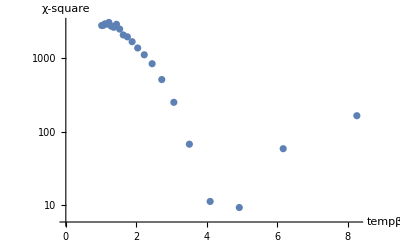

{tempβ,μ,amp,offset,χ-square,μerr,amperr,offseterr}

{4.92611,-0.209882,1584.26,15.7529,9.35378,0.00296521,8.55584,0.874477}

4.92611

-0.209882

1584.26

15.7529

temp (Er): 0.203

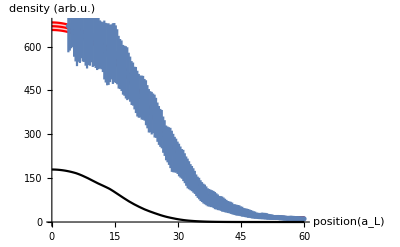

```mathematica
pchi=ListLogPlot[fitls⟦All,{1,5}⟧,AxesLabel->{"tempβ","χ-square"}]
Print[{"tempβ","μ","amp","offset","χ-square","μerr","amperr","offseterr"}]
res=Sort[fitls,#1⟦5⟧<#2⟦5⟧&]⟦1⟧
tempβfit=res⟦1⟧
μfit=res⟦2⟧
ampfit=res⟦3⟧
offsetfit=res⟦4⟧

Print[StringJoin["temp (Er): ",ToString[1/tempβfit]]]

tempβcheck=tempβfit;
Tβlist= Select[result,#⟦1⟧==tempβcheck&]⟦All,1;;6⟧;

densitycheckfunc=Interpolation[Tβlist⟦All,{2,3}⟧];
densityerrcheckfunc=Interpolation[Tβlist⟦All,{2,4}⟧];
doubloncheckfunc=Interpolation[Tβlist⟦All,{2,5}⟧];
doublonerrcheckfunc=Interpolation[Tβlist⟦All,{2,6}⟧];

finalρfunc[positionxx_,μfitxx_,ampxx_,offsetxx_]:=ampxx*(densitycheckfunc[μfitxx-potential[positionxx,f0]]-2doubloncheckfunc[μfitxx-potential[positionxx,f0]])+offsetxx;
finaldoublonfunc[positionxx_,μfitxx_,ampxx_]:=ampxx*doubloncheckfunc[μfitxx-potential[positionxx,f0]];

finalρerrfunc[positionxx_,μfitxx_,ampxx_]:=ampxx*(densityerrcheckfunc[μfitxx-potential[positionxx,f0] ]^2+4 doublonerrcheckfunc[μfitxx-potential[positionxx,f0] ]^2)^0.5;

p1=Show[
Plot[{finalρfunc[x,μfit,ampfit,offsetfit],
finalρfunc[x,μfit,ampfit,offsetfit]-finalρerrfunc[x,μfit,ampfit],
finalρfunc[x,μfit,ampfit,offsetfit]+finalρerrfunc[x,μfit,ampfit]
}
,{x,0,60},PlotStyle->{Red},AxesLabel->{"position(a_L)","density (arb.u.)"},Filling->{2->{3}}]
,ErrorListPlot[datainput],
Plot[finaldoublonfunc[x,μfit,ampfit],{x,0,60},PlotStyle->{Black}]

]
```

4.95636

4.95636

tempβerr =

4.44089×10^-16

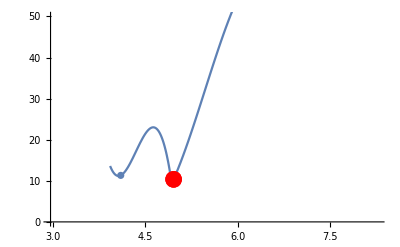

```mathematica
ampfit=res⟦3⟧;

lengdata=Length[datainput];
newchi2=Table[{fitls⟦All,{1,5}⟧⟦ii,1⟧,(fitls⟦All,{1,5}⟧⟦ii,2⟧)/(1+0lengdata)},{ii,1,Length[fitls]}];
newchifitlist=Select[newchi2,#⟦2⟧≤ 500&];
newres=Sort[newchi2,#1⟦2⟧<#2⟦2⟧&]⟦1⟧;
tempβminnew=newres⟦1⟧;
newchifitfunc=Interpolation[newchifitlist];
ffuncg[x_]:=newchifitfunc[X]/.X-> x;
desirechi=Min[newchifitlist⟦All,2⟧]+1;
tempβerrpoint1=FindRoot[ffuncg[x]==desirechi,{x,tempβminnew-0.2}]⟦1,2⟧
tempβerrpoint2=FindRoot[ffuncg[x]==desirechi,{x,tempβminnew+0.2}]⟦1,2⟧
Print["tempβerr = "];
Abs[(tempβerrpoint1-tempβerrpoint2)/2]

Show[ListPlot[newchifitlist,PlotRange->{0,50}],
Plot[ffuncg[x],{x,tempβminnew-1,tempβminnew+1}],ListPlot[{{tempβerrpoint1,desirechi},{tempβerrpoint2,desirechi}},PlotStyle->{PointSize[0.03],Red}]]
```

```mathematica
Export["D:\\Documents\\MC fitting\\2.5Er 206G\\2.5Er 206G.emf",p1,"emf"]
Export["D:\\Documents\\MC fitting\\2.5Er 206G\\2.5Er 206G pchi.emf",pchi,"emf"]
```

D:\Documents\MC fitting\2.5Er 206G\2.5Er 206G.emf

D:\Documents\MC fitting\2.5Er 206G\2.5Er 206G pchi.emf

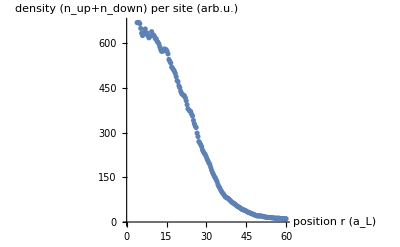

2.45098

-0.892027

1375.13

-2.02053

temp (Er): 0.408

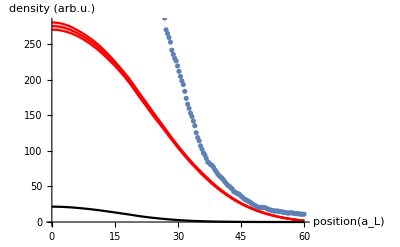

```mathematica
startid=12;

rawdatatemp=ToExpression[Import["D:\\Documents\\MC fitting\\2.5Er 206G\\temp.txt","TSV"]];

datainput1=Table[{rawdatatemp⟦ii,1⟧(0.18μm)/(λlat/2),rawdatatemp⟦ii,2⟧},{ii,startid,Length[rawdatatemp]}];
datainput=Select[datainput1,#⟦1⟧≤ 60&];
ListPlot[datainput,AxesLabel->{"position r (a_L)","density (n_up+n_down) per site (arb.u.)"}]
(*MC data input*)
path=NotebookDirectory[];
path=StringJoin[path,"\\results.txt"];
resulttemp=ToExpression[Import[path,"TSV"]];
result=resulttemp;
tempβlist=Union[result⟦All,1⟧];
tempβnum=Length[tempβlist];


res={2.450980392156863,-0.8920269224441666,1375.1253165574878,-2.020533916578205,0.001195010567193326,0.016650780999035927,41.687077353316475,0.6330609008499594};
tempβfit=res⟦1⟧
μfit=res⟦2⟧
ampfit=res⟦3⟧
offsetfit=res⟦4⟧

Print[StringJoin["temp (Er): ",ToString[1/tempβfit]]]

tempβcheck=tempβfit;
Tβlist= Select[result,#⟦1⟧==tempβcheck&]⟦All,1;;6⟧;

densitycheckfunc=Interpolation[Tβlist⟦All,{2,3}⟧];
densityerrcheckfunc=Interpolation[Tβlist⟦All,{2,4}⟧];
doubloncheckfunc=Interpolation[Tβlist⟦All,{2,5}⟧];
doublonerrcheckfunc=Interpolation[Tβlist⟦All,{2,6}⟧];

finalρfunc[positionxx_,μfitxx_,ampxx_,offsetxx_]:=ampxx*(densitycheckfunc[μfitxx-potential[positionxx,f0]]-2doubloncheckfunc[μfitxx-potential[positionxx,f0]])+offsetxx;
finaldoublonfunc[positionxx_,μfitxx_,ampxx_]:=ampxx*doubloncheckfunc[μfitxx-potential[positionxx,f0]];

finalρerrfunc[positionxx_,μfitxx_,ampxx_]:=ampxx*(densityerrcheckfunc[μfitxx-potential[positionxx,f0] ]^2+4 doublonerrcheckfunc[μfitxx-potential[positionxx,f0] ]^2)^0.5;

p1=Show[
Plot[{finalρfunc[x,μfit,ampfit,offsetfit],
finalρfunc[x,μfit,ampfit,offsetfit]-finalρerrfunc[x,μfit,ampfit],
finalρfunc[x,μfit,ampfit,offsetfit]+finalρerrfunc[x,μfit,ampfit]
}
,{x,0,60},PlotStyle->{Red},AxesLabel->{"position(a_L)","density (arb.u.)"},Filling->{2->{3}}]
,ListPlot[datainput],
Plot[finaldoublonfunc[x,μfit,ampfit],{x,0,60},PlotStyle->{Black}]

]
```

## New demarco density err calculation

temp (Er): 0.326

{tempβfit,tempβfiterr,μfit,μfiterr}

{3.06748,0.441287,-0.591606,0.0109689}

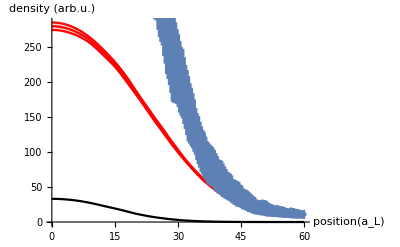

```mathematica
startid=7;
endid=60;

rawdatatemp=ToExpression[Import["D:\\Documents\\MC fitting\\2.5Er 206G\\temp.txt","TSV"]];

datainput1=Table[{rawdatatemp⟦ii,1⟧(0.18μm)/(λlat/2),rawdatatemp⟦ii,2⟧,rawdatatemp⟦ii,3⟧},{ii,startid,Length[rawdatatemp]}];
datainput=Select[datainput1,(#⟦1⟧≤ endid&&#⟦1⟧≥ startid)&];
(*ListPlot[datainput,AxesLabel->{"position r (a_L)","density (n_up+n_down) per site (arb.u.)"}]*)
(*MC data input*)
path=NotebookDirectory[];
path=StringJoin[path,"\\results.txt"];
resulttemp=ToExpression[Import[path,"TSV"]];
result=resulttemp;
tempβlist=Union[result⟦All,1⟧];
tempβnum=Length[tempβlist];


res={3.067484662576687,-0.5916059418019215,1000.0000039525848,7.250957081474479,2.6640246734200006,0.010968897125284425,21.174451537097287,0.6450085201942946};

tempβfit=res⟦1⟧;
μfit=res⟦2⟧;
ampfit=res⟦3⟧;
offsetfit=res⟦4⟧;
μfiterr=res⟦6⟧;
Print[StringJoin["temp (Er): ",ToString[1/tempβfit]]];
tempβcheck=tempβfit;
tempβerrlisttemp=Sort[tempβlist,Abs[#1-tempβfit]≤ Abs[#2-tempβfit]&];
tempβfiterr=Max[Abs[tempβerrlisttemp⟦3⟧-tempβerrlisttemp⟦1⟧],Abs[tempβerrlisttemp⟦2⟧-tempβerrlisttemp⟦1⟧]];
Print[{"tempβfit","tempβfiterr","μfit","μfiterr"}];
Print[{tempβfit,tempβfiterr,μfit,μfiterr}];
Tβlist= Select[result,#⟦1⟧==tempβcheck&]⟦All,1;;6⟧;
densitycheckfunc=Interpolation[Tβlist⟦All,{2,3}⟧];
densityerrcheckfunc=Interpolation[Tβlist⟦All,{2,4}⟧];
doubloncheckfunc=Interpolation[Tβlist⟦All,{2,5}⟧];
doublonerrcheckfunc=Interpolation[Tβlist⟦All,{2,6}⟧];

finalρfunc[positionxx_,μfitxx_,ampxx_,offsetxx_]:=ampxx*(densitycheckfunc[μfitxx-potential[positionxx,f0]]-2doubloncheckfunc[μfitxx-potential[positionxx,f0]])+offsetxx;
finaldoublonfunc[positionxx_,μfitxx_,ampxx_]:=ampxx*doubloncheckfunc[μfitxx-potential[positionxx,f0]];

finalρerrfunc[positionxx_,μfitxx_,ampxx_]:=ampxx*(densityerrcheckfunc[μfitxx-potential[positionxx,f0] ]^2+4 doublonerrcheckfunc[μfitxx-potential[positionxx,f0] ]^2)^0.5;

p1=Show[
Plot[{finalρfunc[x,μfit,ampfit,offsetfit],
finalρfunc[x,μfit,ampfit,offsetfit]-finalρerrfunc[x,μfit,ampfit],
finalρfunc[x,μfit,ampfit,offsetfit]+finalρerrfunc[x,μfit,ampfit]
}
,{x,0,60},PlotStyle->{Red},AxesLabel->{"position(a_L)","density (arb.u.)"},Filling->{2->{3}}]
,ErrorListPlot[datainput],
Plot[finaldoublonfunc[x,μfit,ampfit],{x,0,60},PlotStyle->{Black}]

]

(*3D trap frequencies*)
f0horizontal=f0;
f0vertical=√(fz^2+(xdtfreq*200/30)^2);
vext[ix_,iy_,iz_]:=1/2 massK40 ((2π f0horizontal)^2(ix^2+iy^2)(λlat/2)^2+(2π f0vertical)^2 iz^2 (λlat/2)^2)/Erecoil;
dx=1;
dy=1;
dz=1;
```

### density weighted density and err calculation

{0.136081,0.0076986}

{0.137591,0.00786515}

{0.139113,0.00803466}

{0.140648,0.00820718}

{0.142196,0.00838275}

{0.143757,0.00856149}

0.346884+0.349872 x

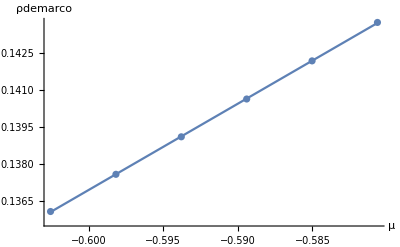

0.0313931+0.0393305 x

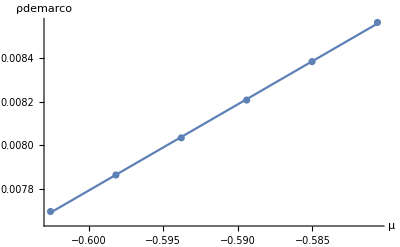

```mathematica
(*calculate μ related err slope*)
iiμlength=5;
μrelatederrslopelist={0};
For[iiμ=1,iiμ≤ iiμlength+1,iiμ++,
{
(*find corresponding μ and temp list*)
μchecktemp=(μfit-μfiterr)+(iiμ-1)*(2 μfiterr)/iiμlength;
tempβcheck=tempβfit;
(*find corresponding μ and temp list*)
(*data interpolation*)
Tβlist= Select[result,#⟦1⟧==tempβcheck&]⟦All,1;;6⟧;
densitycheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,3}⟧]];
densityerrcheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,4}⟧]];
doubloncheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,5}⟧]];
doublonerrcheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,6}⟧]];

finalρfunc[positionxx_,μfitxx_,ampxx_,offsetxx_]:=Quiet[ampxx*(densitycheckfunc[μfitxx-potential[positionxx,f0]]-2doubloncheckfunc[μfitxx-potential[positionxx,f0]])+offsetxx];
finaldoublonfunc[positionxx_,μfitxx_,ampxx_]:=Quiet[ampxx*doubloncheckfunc[μfitxx-potential[positionxx,f0]]];

finalρerrfunc[positionxx_,μfitxx_,ampxx_]:=Quiet[ampxx*(densityerrcheckfunc[μfitxx-potential[positionxx,f0] ]^2+4 doublonerrcheckfunc[μfitxx-potential[positionxx,f0] ]^2)^0.5];
finaldoublonerrfunc[positionxx_,μfitxx_,ampxx_]:=Quiet[ampxx*doublonerrcheckfunc[μfitxx-potential[positionxx,f0]]];
(*data interpolation*)

(*calculated demarco density err*)
iixmax=40;
iiymax=40;
iizmax=20;
finalρfunc3d[iix_,iiy_,iiz_]:=Quiet[densitycheckfunc[μchecktemp-vext[iix,iiy,iiz]]];
finaldoublon3d[iix_,iiy_,iiz_]:=Quiet[doubloncheckfunc[μchecktemp-vext[iix,iiy,iiz]]];

final3dρlist=Table[{iix,iiy,iiz,Max[0,finalρfunc3d[iix,iiy,iiz]]},{iix,0,iixmax,dx},{iiy,0,iiymax,dy},{iiz,0,iizmax,dz}];
final3ddoublonlist=Table[{iix,iiy,iiz,Max[0,finaldoublon3d[iix,iiy,iiz]]},{iix,0,iixmax,dx},{iiy,0,iiymax,dy},{iiz,0,iizmax,dz}];

dimls=Dimensions[final3dρlist];
dimlsleng=dimls⟦1⟧*dimls⟦2⟧*dimls⟦3⟧;
ls3dρ=ArrayReshape[final3dρlist,{dimlsleng,4}];
ls3ddoublon=ArrayReshape[final3ddoublonlist,{dimlsleng,4}];
ρdemarcon2=Total[Table[ls3dρ⟦ii,4⟧^2,{ii,1,Length[ls3dρ]}]];
doublondemarcon2=Total[Table[ls3dρ⟦ii,4⟧*ls3ddoublon⟦ii,4⟧,{ii,1,Length[ls3dρ]}]];
ntot=Total[ls3dρ⟦All,4⟧];
ρdemarco=ρdemarcon2/ntot;
doublondemarco=doublondemarcon2/ntot;
Print[{ρdemarco,doublondemarco}];
μrelatederrslopelisttemp={{μchecktemp,ρdemarco,doublondemarco}};
μrelatederrslopelist=Join[μrelatederrslopelist,μrelatederrslopelisttemp];
(*calculated demarco density err*)
}
]
μrelatederrslopelistfinal=μrelatederrslopelist⟦2;;iiμlength+2,{1,2}⟧;
sol=Fit[μrelatederrslopelistfinal,{1,x},x]
Show[ListPlot[μrelatederrslopelistfinal,AxesLabel->{"μ","ρdemarco"}],Plot[sol,{x,μfit-μfiterr,μfit+μfiterr}]]
μrelatedslope=sol⟦2,1⟧;

μrelateddoublonerrslopelistfinal=μrelatederrslopelist⟦2;;iiμlength+2,{1,3}⟧;
soldoublon1=Fit[μrelateddoublonerrslopelistfinal,{1,x},x]
Show[ListPlot[μrelateddoublonerrslopelistfinal,AxesLabel->{"μ","ρdemarco"}],Plot[soldoublon1,{x,μfit-μfiterr,μfit+μfiterr}]]
μrelateddoublonslope=soldoublon1⟦2,1⟧;
```

{{3.06748,0.139879,0.00812055}}

{{2.7248,0.160866,0.0104114}}

{{3.50877,0.118588,0.00597056}}

0.306145-0.0536608 x

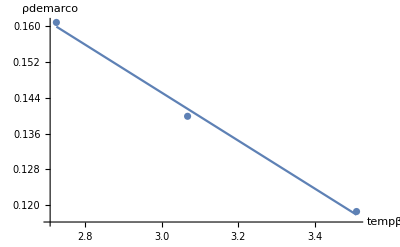

0.0256142-0.00562732 x

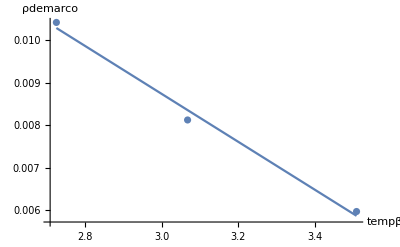

```mathematica
(*calculate tempβ related err slope*)
iitempβlength=3;
tempβrelatederrslopelist={0};
For[iitempβ=1,iitempβ≤ iitempβlength,iitempβ++,
{
(*find corresponding μ and temp list*)
μchecktemp=μfit;
tempβcheck=tempβerrlisttemp⟦iitempβ⟧;
(*find corresponding μ and temp list*)
(*data interpolation*)
Tβlist= Select[result,#⟦1⟧==tempβcheck&]⟦All,1;;6⟧;
densitycheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,3}⟧]];
densityerrcheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,4}⟧]];
doubloncheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,5}⟧]];
doublonerrcheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,6}⟧]];
finalρfunc[positionxx_,μfitxx_,ampxx_,offsetxx_]:=Quiet[ampxx*(densitycheckfunc[μfitxx-potential[positionxx,f0]]-2doubloncheckfunc[μfitxx-potential[positionxx,f0]])+offsetxx];
finaldoublonfunc[positionxx_,μfitxx_,ampxx_]:=Quiet[ampxx*doubloncheckfunc[μfitxx-potential[positionxx,f0]]];

finalρerrfunc[positionxx_,μfitxx_,ampxx_]:=Quiet[ ampxx*(densityerrcheckfunc[μfitxx-potential[positionxx,f0]  ]^2+4 doublonerrcheckfunc[μfitxx-potential[positionxx,f0]  ]^2)^0.5]; 
(*data interpolation*)

(*calculated demarco density err*)
iixmax=40;
iiymax=40;
iizmax=20;
finalρfunc3d[iix_,iiy_,iiz_]:=Quiet[densitycheckfunc[μchecktemp-vext[iix,iiy,iiz]]];
final3dρlist=Table[{iix,iiy,iiz,Max[0,finalρfunc3d[iix,iiy,iiz]]},{iix,0,iixmax,dx},{iiy,0,iiymax,dy},{iiz,0,iizmax,dz}];
final3ddoublonlist=Table[{iix,iiy,iiz,Max[0,finaldoublon3d[iix,iiy,iiz]]},{iix,0,iixmax,dx},{iiy,0,iiymax,dy},{iiz,0,iizmax,dz}];
dimls=Dimensions[final3dρlist];
dimlsleng=dimls⟦1⟧*dimls⟦2⟧*dimls⟦3⟧;
ls3dρ=ArrayReshape[final3dρlist,{dimlsleng,4}];
ls3ddoublon=ArrayReshape[final3ddoublonlist,{dimlsleng,4}];
ρdemarcon2=Total[Table[ls3dρ⟦ii,4 ⟧^2,{ii,1,Length[ls3dρ]}]];
ntot=Total[ls3dρ⟦All,4⟧];
ρdemarco=ρdemarcon2/ntot;
doublondemarcon2=Total[Table[ls3dρ⟦ii,4⟧*ls3ddoublon⟦ii,4⟧,{ii,1,Length[ls3dρ]}]];
doublondemarco=doublondemarcon2/ntot;
tempβrelatederrslopelisttemp={{tempβcheck,ρdemarco,doublondemarco}};
Print[tempβrelatederrslopelisttemp];
tempβrelatederrslopelist=Join[tempβrelatederrslopelist,tempβrelatederrslopelisttemp]; 
(*calculated demarco density err*)
}
]
tempβrelatederrslopelistfinal=tempβrelatederrslopelist⟦2;;iitempβlength+1,{1,2}⟧;
soltempβ=Fit[tempβrelatederrslopelistfinal,{1,x},x]
Show[ListPlot[tempβrelatederrslopelistfinal,AxesLabel->{"tempβ","ρdemarco"}],Plot[soltempβ,{x,Min[tempβerrlisttemp⟦1;;3⟧],Max[tempβerrlisttemp⟦1;;3⟧]}]]
tempβrelatedslope=soltempβ⟦2,1⟧;

tempβrelateddoublonerrslopelistfinal=tempβrelatederrslopelist⟦2;;iitempβlength+1,{1,3}⟧;
soltempβdoublon=Fit[tempβrelateddoublonerrslopelistfinal,{1,x},x]
Show[ListPlot[tempβrelateddoublonerrslopelistfinal,AxesLabel->{"tempβ","ρdemarco"}],Plot[soltempβdoublon,{x,Min[tempβerrlisttemp⟦1;;3⟧],Max[tempβerrlisttemp⟦1;;3⟧]}]]
tempβrelateddoublonslope=soltempβdoublon⟦2,1⟧;
```

```mathematica
f0horizontal=f0;
f0vertical=√(fz^2+(xdtfreq*200/30)^2);
vext[ix_,iy_,iz_]:=1/2 massK40 ((2π f0horizontal)^2(ix^2+iy^2)(λlat/2)^2+(2π f0vertical)^2 iz^2 (λlat/2)^2)/Erecoil;
dx=1;
dy=1;
dz=1;
tempβcheck=tempβfit;
Tβlist= Select[result,#⟦1⟧==tempβcheck&]⟦All,1;;6⟧;
densitycheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,3}⟧]];
densityerrcheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,4}⟧]];
doubloncheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,5}⟧]];
doublonerrcheckfunc=Quiet[Interpolation[Tβlist⟦All,{2,6}⟧]];

finalρfunc3d[iix_,iiy_,iiz_]:=densitycheckfunc[μfit-vext[iix,iiy,iiz]];
finalρerrfunc3d[iix_,iiy_,iiz_]:=densityerrcheckfunc[μfit-vext[iix,iiy,iiz]];
doublonρfunc3d[iix_,iiy_,iiz_]:=doubloncheckfunc[μfit-vext[iix,iiy,iiz]];
doublonρerrfunc3d[iix_,iiy_,iiz_]:=doublonerrcheckfunc[μfit-vext[iix,iiy,iiz]];

iixmax=40;
iiymax=40;
iizmax=20;
final3dρlist=Quiet[Table[{iix,iiy,iiz,Max[0,finalρfunc3d[iix,iiy,iiz]]},{iix,0,iixmax,dx},{iiy,0,iiymax,dy},{iiz,0,iizmax,dz}]];
final3dρerrlist=Quiet[Table[{iix,iiy,iiz,Max[0,Abs[finalρerrfunc3d[iix,iiy,iiz]]]},{iix,0,iixmax,dx},{iiy,0,iiymax,dy},{iiz,0,iizmax,dz}]];
final3ddoublonlist=Quiet[Table[{iix,iiy,iiz,Max[0,doublonρfunc3d[iix,iiy,iiz]]},{iix,0,iixmax,dx},{iiy,0,iiymax,dy},{iiz,0,iizmax,dz}]];
final3ddoublonerrlist=Quiet[Table[{iix,iiy,iiz,Max[0,doublonρerrfunc3d[iix,iiy,iiz]]},{iix,0,iixmax,dx},{iiy,0,iiymax,dy},{iiz,0,iizmax,dz}]];

dimls=Dimensions[final3dρlist];
dimlsleng=dimls⟦1⟧*dimls⟦2⟧*dimls⟦3⟧;
ls3dρ=ArrayReshape[final3dρlist,{dimlsleng,4}];
ls3dρerr=ArrayReshape[final3dρerrlist,{dimlsleng,4}];
ls3ddoublon=ArrayReshape[final3ddoublonlist,{dimlsleng,4}];
ls3ddoublonerr=ArrayReshape[final3ddoublonerrlist,{dimlsleng,4}];
ρdemarcon2=Total[Table[ls3dρ⟦ii,4⟧^2,{ii,1,Length[ls3dρ]}]];
nsquaretot=ρdemarcon2;
ntot=Total[ls3dρ⟦All,4⟧];
dbtot=Total[ls3ddoublon⟦All,4⟧*ls3dρ⟦All,4⟧];

lsρdemarcoerr= Table[(((2*ls3dρ⟦ii,4⟧)/ntot+nsquaretot/ntot^2)ls3dρerr⟦ii,4⟧)^2,{ii,1,Length[ls3dρ]}];
lsdoublongdemarcoerr1=Table[
(
((ls3ddoublonerr⟦ii,4⟧*ls3dρ⟦ii,4⟧)/ntot)^2+((ls3ddoublon⟦ii,4⟧*ls3dρerr⟦ii,4⟧)/ntot)^2+((ls3ddoublon⟦ii,4⟧*ls3dρ⟦ii,4⟧)/ntot^2)^2
),{ii,1,Length[ls3dρ]}];

dbcenterfraction=doublonρfunc3d[0,0,0]/finalρfunc3d[0,0,0];
dbfraction=Total[ls3ddoublon⟦All,4⟧]/ntot;


Print[StringJoin["center doublon fraction:   ", ToString[dbcenterfraction]]];
Print[StringJoin["total doublon fraction:   ", ToString[dbfraction]]];

ntot=Total[ls3dρ⟦All,4⟧];

ρdemarco=nsquaretot/ntot;
dbdemarco=dbtot/ntot;
ρdemarcoerr=Sqrt[Total[lsρdemarcoerr]+(tempβrelatedslope *√(tempβfiterr^2+(0.04 tempβfit^2)^2))^2+(μrelatedslope*μfiterr)^2];
dbdemarcoerr=Sqrt[Total[lsdoublongdemarcoerr1]+(tempβrelateddoublonslope *(tempβfiterr+0.04 tempβfit^2))^2+(μrelateddoublonslope*μfiterr)^2];
Print[StringJoin["density weighted doublon:",ToString[dbdemarco]]];
Print["density weighted doublon errbar:"]
dbdemarcoerr
Print[StringJoin["density weighted density:   ", ToString[ρdemarco]]];
Print["density weighted density errbar:"];
ρdemarcoerr
```

center doublon fraction:   0.0977845

total doublon fraction:   0.041285

density weighted doublon:0.00812055

density weighted doublon errbar:

0.00462145

density weighted density:   0.139879

density weighted density errbar:

0.0313589

## Calculate 3-D density

```mathematica
f0horizontal=f0;
f0vertical=√(fz^2+(xdtfreq*200/30)^2);
vext[ix_,iy_,iz_]:=1/2 massK40 ((2π f0horizontal)^2(ix^2+iy^2)(λlat/2)^2+(2π f0vertical)^2 iz^2 (λlat/2)^2)/Erecoil;
dx=1;
dy=1;
dz=1;
finalρfunc3d[iix_,iiy_,iiz_]:=densitycheckfunc[μfit-vext[iix,iiy,iiz]];
finalρerrfunc3d[iix_,iiy_,iiz_]:=densityerrcheckfunc[μfit-vext[iix,iiy,iiz]];
doublonρfunc3d[iix_,iiy_,iiz_]:=doubloncheckfunc[μfit-vext[iix,iiy,iiz]];

final3dρlist=Table[{iix,iiy,iiz,Max[0,finalρfunc3d[iix,iiy,iiz]]},{iix,0,80,dx},{iiy,0,80,dy},{iiz,0,40,dz}];
final3dρerrlist1=Table[{iix,iiy,iiz,(2Max[0,finalρfunc3d[iix,iiy,iiz]]*Max[0,Abs[finalρerrfunc3d[iix,iiy,iiz]]])^2},{iix,0,80,dx},{iiy,0,80,dy},{iiz,0,40,dz}];
final3dρerrlist2=Table[{iix,iiy,iiz,(Max[0,Abs[finalρerrfunc3d[iix,iiy,iiz]]])^2},{iix,0,80,dx},{iiy,0,80,dy},{iiz,0,40,dz}];
final3ddoublonlist=Table[{iix,iiy,iiz,Max[0,doublonρfunc3d[iix,iiy,iiz]]},{iix,0,80,dx},{iiy,0,80,dy},{iiz,0,40,dz}];


dimls=Dimensions[final3dρlist];
dimlsleng=dimls⟦1⟧*dimls⟦2⟧*dimls⟦3⟧;
ls3dρ=ArrayReshape[final3dρlist,{dimlsleng,4}];
ls3dρerr1=ArrayReshape[final3dρerrlist1,{dimlsleng,4}];
ls3dρerr2=ArrayReshape[final3dρerrlist2,{dimlsleng,4}];
ls3ddoublon=ArrayReshape[final3ddoublonlist,{dimlsleng,4}];


dbcenterfraction=doublonρfunc3d[0,0,0]/finalρfunc3d[0,0,0];
dbfraction=Total[ls3ddoublon⟦All,4⟧]/Total[ls3dρ⟦All,4⟧];
Print[StringJoin["center doublon fraction:   ", ToString[dbcenterfraction]]];
Print[StringJoin["total doublon fraction:   ", ToString[dbfraction]]];
ρdemarcon2=Total[Table[ls3dρ⟦ii,4⟧^2,{ii,1,Length[ls3dρ]}]];
ntot=Total[ls3dρ⟦All,4⟧];

ρdemarco=ρdemarcon2/ntot;
ρdemarcoerr=Sqrt[Total[ls3dρerr1⟦All,4⟧]/ρdemarcon2^2+Total[ls3dρerr2⟦All,4⟧]/ntot^2]ρdemarco;
Print[StringJoin["density weighted density:   ", ToString[ρdemarco]]];
Print["density weighted density errbar:"];
ρdemarcoerr*10^5
```

InterpolatingFunction::dmval: Input value {-7.2159} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-7.62345} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-8.04317} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-7.2159} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-7.62345} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-7.2159} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-7.62345} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-8.04317} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-7.2159} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-7.62345} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-8.04317} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

center doublon fraction:   0.0977845

total doublon fraction:   0.0394272

density weighted density:   0.133565

density weighted density errbar:

6.09301

```mathematica
Export["D:\\Documents\\MC fitting\\2.5Er 206G\\2.5Er 206G density.txt", ls3dρ, "TSV"]
Export["D:\\Documents\\MC fitting\\2.5Er 206G\\2.5Er 206G density error.txt", ls3dρerr, "TSV"]
Export["D:\\Documents\\MC fitting\\2.5Er 206G\\2.5Er 206G doublon.txt", ls3ddoublon, "TSV"]
```

D:\Documents\MC fitting\2.5Er 206G\2.5Er 206G density.txt

D:\Documents\MC fitting\2.5Er 206G\2.5Er 206G density error.txt

D:\Documents\MC fitting\2.5Er 206G\2.5Er 206G doublon.txt